```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle_normal.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
(* Check data *)
Position[filled,0.]
Position[washed,0.]
```

```mathematica
{}
```

{}

```mathematica
Length[filled]
Length[washed]
```

9744

6214

```mathematica
fitCellSizeFromOrganelles[dataset_]:=Module[
{expr,a,b,c,alpha,mean,n,nlm,params,fittedFunc,fitted,fittedMin,fittedMax,dataMin,dataMax},
expr = Sum[a[i]n[i]mean[i]^alpha[i],{i,1,6}]+Sum[n[i]mean[i]^alpha[i]b[i,j]n[j]mean[j]^alpha[j],{i,1,6},{j,i,6}]+c;
nlm = NonlinearModelFit[
dataset[[All,2;;]],expr,
Join[
Table[a[i],{i,1,6}],
Flatten[Table[b[i,j],{i,1,6},{j,i,6}]],
{c},
Table[alpha[i],{i,1,6}]
],
Join[
Table[mean[i],{i,1,6}],
Table[n[i],{i,1,6}]
],
MaxIterations->∞
];
params=nlm["BestFitParameters"];
Print["a[i]: ",Table[a[i],{i,1,6}]/.params];
Print["b[i,j]: ",Table[b[i,j],{i,1,6},{j,1,6}]/.params//MatrixForm];
Print["c: ", c/.params];
Print["alpha[i]: ",Table[alpha[i],{i,1,6}]/.params];
Print["Adjusted R Square: ", nlm["AdjustedRSquared"]];
Print["p-values for parameter z-statistics: ", nlm["ParameterPValues"]];
Print["t-statistics for parameter estimates: ", nlm["ParameterTStatistics"]];
fittedFunc = Function[
vec,
expr/.params
/.Table[n[i]->vec[[i]],{i,1,6}]
/.Table[mean[i]->vec[[i+6]],{i,1,6}]
];
fitted = Map[fittedFunc,dataset[[All,2;;-2]]];
fittedMin = Min[fitted];
fittedMax = Max[fitted];
dataMin = Min[dataset[[All,-1]]];
dataMax = Max[dataset[[All,-1]]];
Print[Show[
ListPlot[
Transpose[{dataset[[All,-1]],fitted}],
PlotTheme->"Scientific"
],
Plot[x,{x,0,dataMax}]
]];
Print[""]
]
```

All Experiments, Null Organelles filled with 0:

a[i]: {0.696729,-9.57666,0.402288,0.4979,1.4033,-0.706302}

b[i,j]: (0.170765 | -0.579225 | -0.139695 | -0.00518762 | 0.260611 | -0.102986
b$11540[2,1] | 10.5245 | -1.18303 | -0.00946476 | -0.172667 | 0.452603
b$11540[3,1] | b$11540[3,2] | 0.393994 | 0.00240183 | -0.328545 | 0.154927
b$11540[4,1] | b$11540[4,2] | b$11540[4,3] | -0.00432734 | 0.0187626 | -0.0257911
b$11540[5,1] | b$11540[5,2] | b$11540[5,3] | b$11540[5,4] | 0.191292 | -0.22388
b$11540[6,1] | b$11540[6,2] | b$11540[6,3] | b$11540[6,4] | b$11540[6,5] | 0.0597549)

c: 37.7287

alpha[i]: {0.925117,0.379822,0.869212,-0.914228,0.689248,1.54461}

Adjusted R Square: 0.962006

p-values for parameter z-statistics: {0.0956655,8.46231×10^-8,0.623104,1.2917×10^-8,5.00977×10^-6,0.163537,1.54544×10^-14,1.8314×10^-11,1.77948×10^-6,0.430493,3.68364×10^-30,0.00146404,3.90237×10^-52,7.36702×10^-8,0.534402,0.00104466,5.87903×10^-7,0.00462498,0.613966,1.05604×10^-9,0.000153857,0.0000151448,4.55863×10^-6,0.000442365,6.06702×10^-88,1.00666×10^-14,0.000500276,7.7456×10^-38,1.85604×10^-194,0.,4.0401×10^-114,2.48635×10^-52,0.,2.45062×10^-26}

t-statistics for parameter estimates: {1.6664,-5.36108,0.491472,5.69205,4.56695,-1.39338,7.69561,-6.72686,-4.77991,-0.788382,11.4497,-3.18263,15.2847,-5.38614,-0.621322,-3.27921,4.99849,2.83271,0.504437,-6.10671,3.78625,-4.32877,4.58674,-3.51463,20.0845,-7.75056,3.48178,12.9134,30.4393,66.2016,23.0099,-15.3147,106.338,10.6494}

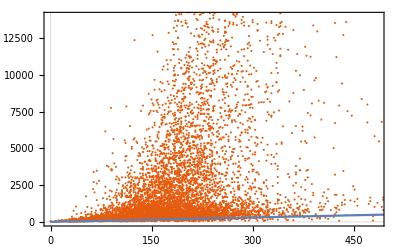

```mathematica
Print["All Experiments, Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[filled];
```

All Experiments, Null Organelles Excluded:

a[i]: {1.43319,-0.631799,-2.43518,0.602025,1.74968,-1.72643}

b[i,j]: (0.095037 | -0.68094 | -0.0506076 | 0.00784741 | 0.134502 | -0.0180395
b$12022[2,1] | 11.5453 | -1.83976 | 0.102965 | -0.485344 | 0.456931
b$12022[3,1] | b$12022[3,2] | 0.758316 | -0.0382842 | -0.376174 | 0.11432
b$12022[4,1] | b$12022[4,2] | b$12022[4,3] | -0.0522034 | 0.109615 | -0.0802438
b$12022[5,1] | b$12022[5,2] | b$12022[5,3] | b$12022[5,4] | 0.147011 | -0.101026
b$12022[6,1] | b$12022[6,2] | b$12022[6,3] | b$12022[6,4] | b$12022[6,5] | 0.0245043)

c: 41.8575

alpha[i]: {0.97367,0.378966,0.810015,-0.203626,0.727264,1.81137}

Adjusted R Square: 0.970595

p-values for parameter z-statistics: {0.0060045,0.842294,0.203612,0.0186789,8.05145×10^-7,0.0107173,0.0000359819,3.40323×10^-10,0.217337,0.673792,1.21553×10^-7,0.626614,2.10451×10^-18,1.11682×10^-6,0.0576047,4.4877×10^-11,0.000962163,0.00613598,0.0644377,5.73774×10^-9,0.0391787,1.47696×10^-12,1.01847×10^-21,0.00582111,2.2024×10^-44,0.00205146,0.204926,7.65658×10^-13,5.4706×10^-118,0.,1.80404×10^-95,0.000133278,0.,1.01369×10^-10}

t-statistics for parameter estimates: {2.74849,-0.198968,-1.27146,2.3525,4.93918,-2.55256,4.1349,-6.28948,-1.23377,0.42097,5.29736,-0.486523,8.77909,-4.87473,1.89905,-6.59886,3.30295,2.74137,-1.84947,-5.83247,2.06274,-7.09128,9.61102,-2.75865,14.0871,-3.08399,1.26778,7.18238,23.601,42.7854,21.098,-3.82273,100.211,6.4761}

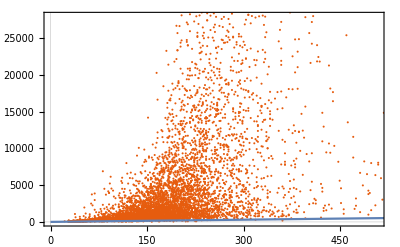

```mathematica
Print["All Experiments, Null Organelles Excluded:"];
fitCellSizeFromOrganelles[washed];
```

EYrainbow_glucose, Null Organelles filled with 0:

a[i]: {7.95055×10^6,-1.87231×10^6,-1.67851×10^7,1.27235×10^7,-899192.,5.71049×10^6}

b[i,j]: (0.206655 | -2.26605 | -7.95056×10^6 | -0.719441 | -0.330848 | 1.98234
b$12504[2,1] | 3.20509 | 1.87232×10^6 | 1.43031 | -0.170369 | -0.855271
b$12504[3,1] | b$12504[3,2] | 673245. | -1.27235×10^7 | 899190. | -5.71051×10^6
b$12504[4,1] | b$12504[4,2] | b$12504[4,3] | -0.0905509 | -0.0507523 | -1.10097
b$12504[5,1] | b$12504[5,2] | b$12504[5,3] | b$12504[5,4] | 0.145153 | -0.237671
b$12504[6,1] | b$12504[6,2] | b$12504[6,3] | b$12504[6,4] | b$12504[6,5] | 0.279037)

c: 1.6112×10^7

alpha[i]: {0.711231,0.472112,-1.01925×10^-6,0.528598,0.857688,0.518671}

Adjusted R Square: 0.957991

p-values for parameter z-statistics: {0.,0.,0.,0.,0.,0.,0.558229,0.0000385444,0.,0.0349717,0.0286449,0.00161899,0.0150112,0.,0.000040135,0.150444,0.0277493,0.,0.,0.,0.,0.482971,0.569478,0.00805373,0.000044358,0.0599673,0.221337,0.,6.81699×10^-23,1.44105×10^-40,2.46376×10^-16,1.09666×10^-6,1.96383×10^-186,0.0117437}

t-statistics for parameter estimates: {3.51057×10^6,-737628.,-4.00951×10^6,5.29553×10^6,-1.6491×10^6,3.41428×10^6,0.585788,-4.14572,-3.51058×10^6,-2.11328,-2.19341,3.16629,2.43884,737630.,4.13619,-1.43973,-2.20596,160820.,-5.29556×10^6,1.64914×10^6,-3.41429×10^6,-0.701951,-0.569121,-2.65832,4.11253,-1.88445,1.2242,3.8487×10^6,10.2493,14.3474,-8.42551,4.92204,42.4541,2.52717}

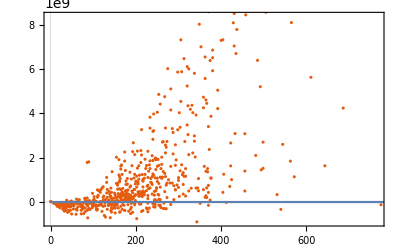

EYrainbow_glucose_largerBF, Null Organelles filled with 0:

a[i]: {-4.81783,16.4708,-162.458,-4.4573,7.03307,8.63351}

b[i,j]: (0.407012 | -4.54289 | 1.91442 | -0.0795996 | 0.095331 | 0.706776
b$12662[2,1] | 17.2503 | -21.7685 | 2.07376 | -0.323612 | 0.194778
b$12662[3,1] | b$12662[3,2] | 88.1717 | 1.82106 | -5.43396 | -2.26305
b$12662[4,1] | b$12662[4,2] | b$12662[4,3] | 0.00428663 | -0.594038 | 0.724965
b$12662[5,1] | b$12662[5,2] | b$12662[5,3] | b$12662[5,4] | 0.359781 | -0.385994
b$12662[6,1] | b$12662[6,2] | b$12662[6,3] | b$12662[6,4] | b$12662[6,5] | 0.0978354)

c: 59.8892

alpha[i]: {0.619894,0.329772,0.279838,1.88814,0.729227,0.494416}

Adjusted R Square: 0.96968

p-values for parameter z-statistics: {0.655467,0.600074,0.665985,0.513876,0.319762,0.168583,0.283156,1.2888×10^-6,0.757159,0.850959,0.665257,0.0509041,0.000417492,0.368162,0.00354378,0.269127,0.669582,0.62403,0.681485,0.335958,0.536978,0.981929,0.000668084,0.0111833,9.15186×10^-18,0.0166275,0.543321,0.757275,1.2395×10^-15,7.60049×10^-27,0.0994903,1.77737×10^-8,4.75916×10^-234,0.00141722}

t-statistics for parameter estimates: {-0.446342,0.524497,-0.43182,-0.653096,0.995545,1.37798,1.07395,-4.87747,0.309316,-0.187953,0.432822,1.95513,3.54318,-0.900414,2.92455,-1.10582,0.426875,0.49033,0.410583,-0.962742,-0.617647,0.0226575,-3.41533,2.54263,8.78171,-2.39973,0.608051,0.309163,8.16034,11.1148,1.64918,5.68858,46.6933,3.20194}

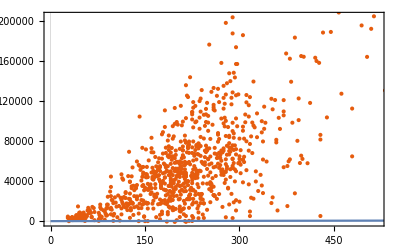

EYrainbow_rapamycin_1stTry, Null Organelles filled with 0:

a[i]: {3.42279,-13.3567,0.685418,-9.61768,7.04366,-2.07536}

b[i,j]: (0.313322 | -0.495174 | -0.018953 | -0.414813 | 0.328839 | -0.360455
b$12800[2,1] | 9.10798 | -0.321376 | 1.47292 | -1.18016 | 0.130376
b$12800[3,1] | b$12800[3,2] | 0.0767022 | -0.0217186 | -0.133651 | -0.0835466
b$12800[4,1] | b$12800[4,2] | b$12800[4,3] | 0.379327 | 0.0985121 | 0.189071
b$12800[5,1] | b$12800[5,2] | b$12800[5,3] | b$12800[5,4] | 0.11439 | 0.0194904
b$12800[6,1] | b$12800[6,2] | b$12800[6,3] | b$12800[6,4] | b$12800[6,5] | 0.216252)

c: 62.5259

alpha[i]: {0.37867,0.403837,1.04573,2.64262,0.303223,0.435492}

Adjusted R Square: 0.953756

p-values for parameter z-statistics: {0.0342084,0.00430735,0.34639,0.00180234,1.17166×10^-6,0.0527066,0.110936,0.218935,0.762829,0.23231,0.100213,0.0053468,0.0000746227,0.21696,0.0174269,0.000169527,0.469685,0.526541,0.786469,0.207605,0.261278,0.169067,0.7128,0.256484,0.293293,0.829232,0.000769661,2.62782×10^-34,0.000779044,4.09033×10^-43,3.98661×10^-9,7.45811×10^-7,2.57607×10^-6,0.00373028}

t-statistics for parameter estimates: {2.11994,-2.85999,0.941971,-3.12776,4.88453,-1.93917,1.59513,-1.22999,-0.301835,-1.19501,1.64504,-2.79027,3.97437,-1.23528,2.38076,-3.77204,0.723212,0.633473,-0.270957,-1.26083,-1.12389,1.37601,0.368183,1.13526,1.05137,0.215732,3.37182,12.5918,3.36845,14.3102,5.92715,4.97451,4.72394,2.90561}

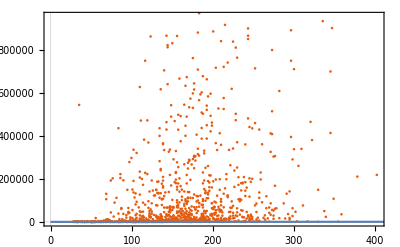

EYrainbow_rapamycin_CheckBistability, Null Organelles filled with 0:

a[i]: {-3.74637,-22.4408,1.73533,4.9535,0.490163,-0.380536}

b[i,j]: (0.219122 | -0.0306399 | -0.232835 | -0.263235 | 0.37083 | -0.274052
b$12938[2,1] | 15.2545 | -2.08231 | 0.34816 | 0.317638 | -0.086636
b$12938[3,1] | b$12938[3,2] | 1.45838 | -1.50555 | -0.886865 | 0.307814
b$12938[4,1] | b$12938[4,2] | b$12938[4,3] | 1.3352 | 0.306796 | 0.284691
b$12938[5,1] | b$12938[5,2] | b$12938[5,3] | b$12938[5,4] | 0.226377 | -0.22029
b$12938[6,1] | b$12938[6,2] | b$12938[6,3] | b$12938[6,4] | b$12938[6,5] | 0.0858692)

c: 34.1267

alpha[i]: {1.01523,0.32123,0.781379,0.629678,0.832371,0.75963}

Adjusted R Square: 0.971839

p-values for parameter z-statistics: {5.13048×10^-7,2.13525×10^-8,0.521037,0.0208712,0.507063,0.601608,2.37029×10^-9,0.842149,0.00870986,0.0241644,2.17033×10^-16,1.4093×10^-9,2.54424×10^-12,0.000139829,0.371839,0.0215657,0.539243,0.0282786,0.000448397,2.0767×10^-6,0.00119048,0.00250105,0.00314945,0.00648853,3.72076×10^-16,3.36409×10^-8,0.000356346,6.13713×10^-10,7.56557×10^-96,1.45827×10^-79,4.84154×10^-54,1.46333×10^-7,0.,2.83143×10^-14}

t-statistics for parameter estimates: {-5.03195,-5.61525,0.641821,2.31148,0.663495,-0.522143,5.98776,-0.199162,-2.6249,-2.25561,8.2576,-6.07276,7.02904,-3.81321,0.893163,2.29909,-0.614026,2.19442,-3.51358,-4.75479,3.24415,3.02568,2.95507,2.72385,8.19158,-5.53533,3.57441,6.20642,21.5157,19.4425,15.7823,5.26922,53.9007,7.64187}

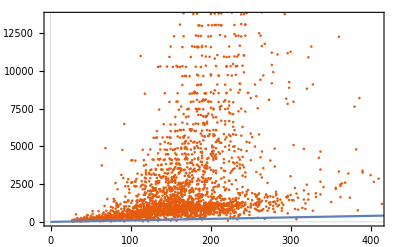

EYrainbow_1nmpp1_1st, Null Organelles filled with 0:

a[i]: {4.1015,-7.49712,2.17978,1.02,3.65027,-4.75357}

b[i,j]: (0.190813 | -0.347852 | -0.0341533 | 0.19114 | -0.0894577 | -0.234675
b$13076[2,1] | 10.3124 | -0.784643 | 1.09945 | -0.182763 | 0.124003
b$13076[3,1] | b$13076[3,2] | 0.116329 | -0.20437 | -0.245506 | 0.010035
b$13076[4,1] | b$13076[4,2] | b$13076[4,3] | 0.0876259 | 0.125328 | 0.234293
b$13076[5,1] | b$13076[5,2] | b$13076[5,3] | b$13076[5,4] | 0.212202 | 0.0369924
b$13076[6,1] | b$13076[6,2] | b$13076[6,3] | b$13076[6,4] | b$13076[6,5] | 0.11108)

c: -8.8883

alpha[i]: {1.17032,0.404532,1.0571,0.0872777,0.715148,0.930041}

Adjusted R Square: 0.969918

p-values for parameter z-statistics: {0.00493782,0.0561456,3.5129×10^-7,0.379877,0.00054923,0.000325854,0.0477486,0.207459,0.400098,0.108,0.334648,0.0616406,8.27744×10^-9,0.00304734,0.000305166,0.357422,0.625858,0.0930838,0.00753064,0.000210796,0.831232,0.164733,0.16541,0.0434917,5.04474×10^-8,0.687586,0.306654,0.15955,6.26302×10^-16,1.58833×10^-94,4.13454×10^-52,0.534286,2.68973×10^-157,0.000791547}

t-statistics for parameter estimates: {2.81496,-1.91129,5.11506,0.878365,3.46249,-3.60163,1.98112,-1.26109,-0.841669,1.60814,-0.965083,-1.87018,5.79354,-2.96744,3.61878,-0.920554,0.487659,1.68035,-2.67581,-3.71423,0.213157,1.38996,1.38774,2.02055,5.47588,0.402205,1.02259,-1.40724,8.16833,22.0748,15.7546,0.62161,29.9908,3.36215}

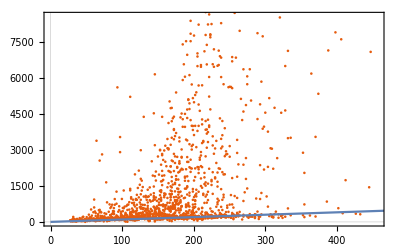

EYrainbow_leucine_large, Null Organelles filled with 0:

a[i]: {0.0049408,0.937427,1.88228,-0.49819,-0.0698077,0.896746}

b[i,j]: (3.45922×10^-8 | 0.0000105572 | -0.0000362882 | -0.000274834 | 0.0000276168 | -0.000499061
b$13214[2,1] | 0.440096 | -0.0983444 | 0.07909 | 0.00596252 | -0.00415221
b$13214[3,1] | b$13214[3,2] | 0.0209771 | -0.0313891 | -0.00131623 | -0.0342072
b$13214[4,1] | b$13214[4,2] | b$13214[4,3] | 0.0292557 | 0.0000688139 | 0.0686443
b$13214[5,1] | b$13214[5,2] | b$13214[5,3] | b$13214[5,4] | 0.0000466083 | 0.00332761
b$13214[6,1] | b$13214[6,2] | b$13214[6,3] | b$13214[6,4] | b$13214[6,5] | 0.0580782)

c: 15.2346

alpha[i]: {4.83104,0.659347,1.15183,0.418643,1.61619,0.305701}

Adjusted R Square: 0.980936

p-values for parameter z-statistics: {0.650029,0.616572,0.00766671,0.359438,0.526426,0.213347,0.843787,0.983403,0.786603,0.626136,0.746296,0.659109,0.111455,0.399697,0.0351601,0.520874,0.916808,0.679908,0.370178,0.584709,0.364169,0.00260943,0.982838,0.0130355,0.740785,0.461298,0.0293473,0.000275306,0.000137445,7.48556×10^-22,1.09958×10^-6,0.110603,0.0000318801,0.00137052}

t-statistics for parameter estimates: {0.453815,0.500821,2.67009,-0.916723,-0.633622,1.24495,0.197087,0.0208061,-0.270773,-0.487275,0.323588,-0.441234,1.59264,-0.842407,2.10846,0.642153,-0.104473,0.41267,-0.896414,-0.546641,-0.907731,3.01551,0.0215145,2.48583,0.330876,0.736905,2.18092,3.64631,3.82281,9.76115,4.89349,1.59645,4.17258,3.20692}

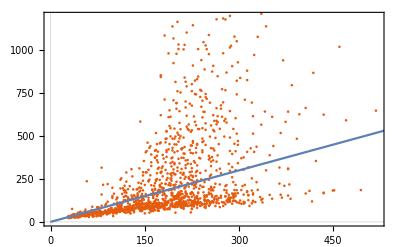

EYrainbowWhi5Up_betaEstrodiol, Null Organelles filled with 0:

a[i]: {10.2175,1.17026,-120.585,7.73935,9.92105,-7.07683}

b[i,j]: (0.239493 | -1.59017 | -2.05651 | 0.0418467 | 0.229477 | -0.341809
b$13352[2,1] | 8.90769 | -1.44567 | 1.36135 | -1.29201 | 0.0498444
b$13352[3,1] | b$13352[3,2] | 35.9827 | -2.94319 | -4.29195 | -0.122284
b$13352[4,1] | b$13352[4,2] | b$13352[4,3] | 0.19809 | -0.119025 | -0.372668
b$13352[5,1] | b$13352[5,2] | b$13352[5,3] | b$13352[5,4] | 0.465209 | -0.0700564
b$13352[6,1] | b$13352[6,2] | b$13352[6,3] | b$13352[6,4] | b$13352[6,5] | 0.813159)

c: 91.2457

alpha[i]: {1.04828,0.412252,0.419638,1.44656,0.704655,1.33722}

Adjusted R Square: 0.981235

p-values for parameter z-statistics: {0.00354431,0.878666,0.416446,0.193492,0.0113249,0.115137,0.00145578,1.145×10^-7,0.153766,0.835776,0.0747082,0.0530184,0.0000179972,0.568837,0.00526238,0.000317945,0.910876,0.417664,0.240857,0.0735164,0.932812,0.322244,0.635695,0.241769,0.00371187,0.771323,0.000812342,0.487042,1.60005×10^-48,8.74393×10^-87,0.0002131,9.79986×10^-6,7.08386×10^-101,1.76366×10^-6}

t-statistics for parameter estimates: {2.92737,0.152724,-0.813149,1.30174,2.54014,-1.57774,3.19778,-5.36525,-1.42811,0.207387,1.78527,-1.9385,4.32232,-0.570071,2.80049,-3.62069,0.111979,0.811024,-1.17398,-1.79266,-0.0843422,0.990651,-0.473961,-1.1717,2.91278,-0.290772,3.3652,0.69544,16.0136,23.3296,3.72515,4.45863,25.9391,4.82532}

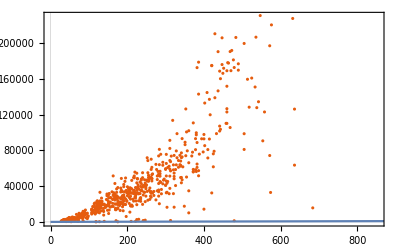

```mathematica
Do[
Print[experiments[[i]],", Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[Select[filled,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
```

EYrainbow_glucose, Null Organelles Excluded:

a[i]: {5.47487,-27.622,0.48096,-3.13462,2.88081×10^-6,3.85831}

b[i,j]: (0.445775 | -2.35577 | -0.0198103 | 0.322307 | -1.78057×10^-7 | 1.03061
b$13819[2,1] | 10.1805 | -0.069881 | 1.98776 | 4.42265×10^-6 | -0.274067
b$13819[3,1] | b$13819[3,2] | 0.000454131 | -0.00992291 | -2.22761×10^-7 | -0.000682103
b$13819[4,1] | b$13819[4,2] | b$13819[4,3] | 0.141132 | -2.35799×10^-7 | -1.00324
b$13819[5,1] | b$13819[5,2] | b$13819[5,3] | b$13819[5,4] | 6.91581×10^-11 | 5.90736×10^-6
b$13819[6,1] | b$13819[6,2] | b$13819[6,3] | b$13819[6,4] | b$13819[6,5] | 0.0202411)

c: 45.0752

alpha[i]: {0.7555,0.394194,1.70892,0.32841,3.04428,0.557125}

Adjusted R Square: 0.97295

p-values for parameter z-statistics: {0.211749,0.0611537,0.221599,0.284506,0.954572,0.37855,0.191762,0.00288126,0.461784,0.415901,0.965293,0.181418,0.0271451,0.429755,0.00747604,0.731161,0.641747,0.696287,0.544998,0.76166,0.938985,0.390977,0.941976,0.114978,0.875476,0.758778,0.939913,0.0913981,2.49285×10^-9,4.6641×10^-26,1.2273×10^-10,0.061419,8.01698×10^-6,0.189896}

t-statistics for parameter estimates: {1.25115,-1.87866,1.22455,-1.07196,0.0570091,0.881732,1.30801,-3.00212,-0.736754,0.814558,-0.0435451,1.33917,2.21911,-0.790564,2.69113,0.343866,-0.465678,0.390671,-0.605887,-0.303547,-0.0766033,0.858953,-0.072841,-1.58029,0.156825,0.307335,0.075435,1.6929,6.12739,11.5041,6.64402,1.87673,4.53502,1.31354}

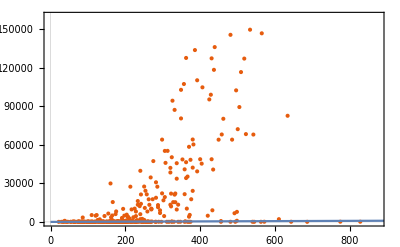

EYrainbow_glucose_largerBF, Null Organelles Excluded:

a[i]: {-45.0484,33.9864,-570.005,-14.5716,24.6618,145.37}

b[i,j]: (-0.436723 | -5.08567 | 30.5792 | -0.103099 | 0.271425 | 7.68666
b$13956[2,1] | 32.2023 | -47.673 | 4.07912 | -1.04797 | -20.3763
b$13956[3,1] | b$13956[3,2] | 360.302 | 9.15637 | -20.7306 | -140.159
b$13956[4,1] | b$13956[4,2] | b$13956[4,3] | -0.0321034 | -0.379627 | 0.808794
b$13956[5,1] | b$13956[5,2] | b$13956[5,3] | b$13956[5,4] | 0.319971 | 3.81128
b$13956[6,1] | b$13956[6,2] | b$13956[6,3] | b$13956[6,4] | b$13956[6,5] | -3.15506)

c: 179.862

alpha[i]: {0.377443,0.282921,0.177476,1.93791,0.768022,3.71759}

Adjusted R Square: 0.974838

p-values for parameter z-statistics: {0.478609,0.756873,0.801825,0.51458,0.523898,0.722741,0.285719,0.00909544,0.589503,0.811379,0.200739,0.60553,0.119859,0.615584,0.0235073,0.0764494,0.59506,0.768026,0.63639,0.555947,0.697689,0.874972,0.0200263,0.86292,5.00346×10^-18,0.634834,0.920422,0.860223,0.0010816,1.0835×10^-7,0.398792,0.000441774,4.68247×10^-205,0.0563117}

t-statistics for parameter estimates: {-0.709021,0.309743,-0.251106,-0.65214,0.637751,0.354978,-1.06859,-2.61763,0.539869,-0.238761,1.28097,0.516758,1.55776,-0.502401,2.27135,-1.77497,-0.531824,0.295103,0.473012,-0.589229,-0.388644,-0.157418,-2.33258,0.172738,8.95724,0.475195,-0.0999479,0.176173,3.28565,5.38272,0.84443,3.53498,49.2848,1.91261}

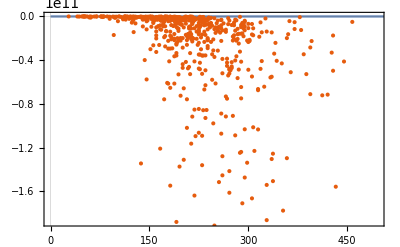

EYrainbow_rapamycin_1stTry, Null Organelles Excluded:

a[i]: {4.73974,-19.7446,-3.30983,-4.34326,10.761,0.257584}

b[i,j]: (0.348908 | -1.13291 | -0.0161668 | -0.525506 | 0.587515 | -0.481935
b$14094[2,1] | 18.5761 | -2.39918 | 2.36921 | -1.7913 | -0.0635328
b$14094[3,1] | b$14094[3,2] | 0.576221 | -0.0925034 | -0.241828 | -0.146956
b$14094[4,1] | b$14094[4,2] | b$14094[4,3] | 0.138856 | -0.0288575 | -0.0377778
b$14094[5,1] | b$14094[5,2] | b$14094[5,3] | b$14094[5,4] | -0.0345846 | -0.0538965
b$14094[6,1] | b$14094[6,2] | b$14094[6,3] | b$14094[6,4] | b$14094[6,5] | 0.271677)

c: 70.2659

alpha[i]: {0.315754,0.349702,0.847956,1.00952,0.0681449,0.729603}

Adjusted R Square: 0.9627

p-values for parameter z-statistics: {0.0775723,0.222994,0.541578,0.0582602,1.91954×10^-8,0.881894,0.122474,0.169235,0.938343,0.0321505,0.00814444,0.00640588,0.0185254,0.126015,0.00307349,0.00307729,0.87877,0.408069,0.538065,0.237553,0.321317,0.292335,0.865514,0.771512,0.781321,0.637003,0.00467298,0.000063441,0.00881426,1.13844×10^-17,2.51326×10^-10,0.00126408,0.553603,0.000741283}

t-statistics for parameter estimates: {1.76733,-1.2196,-0.610703,-1.89658,5.67963,0.148618,1.54619,-1.37597,-0.0773786,-2.14647,2.65298,-2.7338,2.36001,-1.53168,2.96979,-2.9694,-0.152579,0.827753,-0.616021,-1.18205,-0.992399,1.05374,-0.169416,-0.290501,-0.277696,-0.472083,2.83712,4.02202,2.62594,8.77161,6.41218,3.23609,0.592631,3.38758}

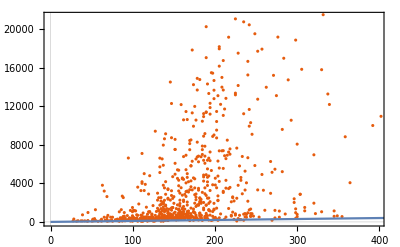

EYrainbow_rapamycin_CheckBistability, Null Organelles Excluded:

a[i]: {-0.23803,2.3262,-4.56638,2.45662,3.33995,-0.438266}

b[i,j]: (0.154752 | -0.610254 | -0.166578 | -0.414718 | 0.278267 | -0.194603
b$14232[2,1] | 9.01304 | -1.895 | 1.34059 | -0.170338 | -0.0102316
b$14232[3,1] | b$14232[3,2] | 1.25754 | -1.27152 | -0.548598 | 0.185579
b$14232[4,1] | b$14232[4,2] | b$14232[4,3] | 1.68252 | 0.232938 | 0.321991
b$14232[5,1] | b$14232[5,2] | b$14232[5,3] | b$14232[5,4] | 0.113859 | -0.144862
b$14232[6,1] | b$14232[6,2] | b$14232[6,3] | b$14232[6,4] | b$14232[6,5] | 0.050741)

c: 18.0912

alpha[i]: {1.09905,0.390899,0.796849,0.857423,0.811011,0.803621}

Adjusted R Square: 0.984654

p-values for parameter z-statistics: {0.734982,0.640192,0.221408,0.393432,6.31154×10^-8,0.532498,1.22048×10^-6,0.000205366,0.0255628,0.00682979,1.55836×10^-10,1.63753×10^-6,0.00241176,0.000809832,0.0201223,0.254784,0.942206,0.0186756,0.00142239,1.49135×10^-7,0.00920578,0.00571894,0.0945132,0.0150476,0.0000895055,0.000383897,0.0194581,0.0942608,5.94301×10^-93,5.3714×10^-33,1.50846×10^-62,2.73864×10^-9,6.2969×10^-196,2.02219×10^-9}

t-statistics for parameter estimates: {-0.338558,0.467509,-1.22321,0.853614,5.43244,-0.624317,4.86878,-3.71992,-2.23464,-2.70814,6.43682,-4.8096,3.03848,-3.35507,2.32612,-1.13917,-0.0725072,2.35407,-3.195,-5.27445,2.60712,2.76678,1.67293,2.43355,3.92627,-3.5576,2.33872,1.67422,21.694,12.2081,17.3576,5.97654,33.9515,6.02675}

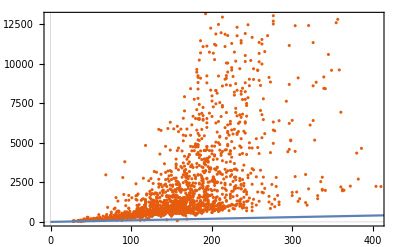

EYrainbow_1nmpp1_1st, Null Organelles Excluded:

a[i]: {3.50591,0.897568,1.61745,2.68903,2.30252,-3.56969}

b[i,j]: (0.00505295 | -0.433991 | -0.122273 | 0.23234 | 0.0869233 | -0.288756
b$14370[2,1] | 8.59915 | -1.41511 | 0.710117 | 0.11164 | -0.336883
b$14370[3,1] | b$14370[3,2] | 0.428631 | -0.621625 | -0.320523 | 0.216963
b$14370[4,1] | b$14370[4,2] | b$14370[4,3] | 0.167718 | 0.260291 | 0.351818
b$14370[5,1] | b$14370[5,2] | b$14370[5,3] | b$14370[5,4] | 0.073592 | -0.117671
b$14370[6,1] | b$14370[6,2] | b$14370[6,3] | b$14370[6,4] | b$14370[6,5] | 0.111619)

c: -6.72342

alpha[i]: {1.25941,0.422415,0.934929,0.208093,0.94193,0.937568}

Adjusted R Square: 0.976039

p-values for parameter z-statistics: {0.0228285,0.883692,0.343123,0.138008,0.00189664,0.0277844,0.952776,0.186502,0.20622,0.0916782,0.152679,0.0513746,0.00457972,0.00597166,0.0484627,0.383931,0.312617,0.0848364,0.00437058,0.000263823,0.0769743,0.080444,0.000884034,0.0162084,0.00456168,0.0860328,0.324016,0.387998,2.38466×10^-9,2.00457×10^-35,1.74046×10^-45,0.0930698,2.58072×10^-104,0.000854772}

t-statistics for parameter estimates: {2.27943,0.146324,0.948413,1.48431,3.11334,-2.20319,0.0592347,-1.32181,-1.26476,1.68806,1.4311,-1.95042,2.84092,-2.75459,1.97544,0.871017,-1.0102,1.72481,-2.8559,-3.66012,1.77015,1.7497,3.334,2.40783,2.84219,-1.71822,0.986673,-0.86359,6.01823,12.8638,14.8146,1.68085,24.181,3.34345}

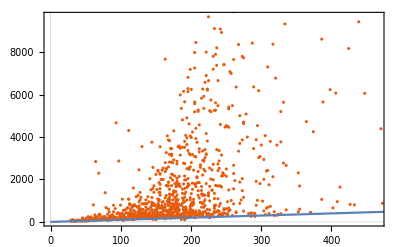

EYrainbow_leucine_large, Null Organelles Excluded:

a[i]: {0.0563306,2.04486,1.15134,1.65373,0.244904,0.814932}

b[i,j]: (-0.0657253 | -0.261834 | 0.010063 | -0.0555318 | 0.24793 | -0.156858
b$14508[2,1] | 0.929668 | -0.0553148 | 0.0494852 | -0.163582 | -0.0452303
b$14508[3,1] | b$14508[3,2] | 0.0080651 | -0.00809441 | -0.0222354 | -0.0125062
b$14508[4,1] | b$14508[4,2] | b$14508[4,3] | -0.00480908 | -0.0798616 | 0.0784637
b$14508[5,1] | b$14508[5,2] | b$14508[5,3] | b$14508[5,4] | 0.14583 | -0.139182
b$14508[6,1] | b$14508[6,2] | b$14508[6,3] | b$14508[6,4] | b$14508[6,5] | 0.132638)

c: 8.73153

alpha[i]: {-0.644591,0.594088,1.25099,-0.823046,0.545933,0.394545}

Adjusted R Square: 0.983538

p-values for parameter z-statistics: {0.96106,0.452549,0.181731,0.0117347,0.847813,0.362646,0.286113,0.0835603,0.661097,0.149357,0.0160564,0.0648707,0.163819,0.600998,0.307907,0.155351,0.530069,0.802593,0.622129,0.600027,0.610315,0.682608,0.059487,0.0134385,0.0041345,0.0718114,0.00907382,0.362869,0.000984223,3.19194×10^-15,0.00154247,2.01986×10^-8,1.17755×10^-9,0.000600029}

t-statistics for parameter estimates: {0.0488385,0.751528,1.33657,2.52565,0.19197,0.91084,-1.06738,-1.73249,0.438557,-1.44315,2.4126,-1.84862,1.39358,-0.523167,1.02026,-1.42218,-0.628165,0.250073,-0.493021,-0.524564,-0.509818,-0.409052,-1.88718,2.47727,2.87575,-1.80263,2.61545,0.910415,-3.30688,8.03648,3.17719,-5.66597,6.15403,3.44493}

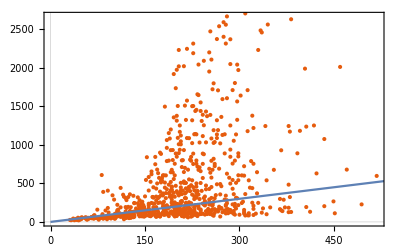

EYrainbowWhi5Up_betaEstrodiol, Null Organelles Excluded:

a[i]: {4.54891,20.3794,-296.475,6.26267,14.5556,-16.4669}

b[i,j]: (0.146396 | -1.10991 | -0.669914 | 0.119984 | 0.168517 | -0.401359
b$14646[2,1] | 6.04524 | -6.56303 | 1.24744 | -0.954179 | 0.364823
b$14646[3,1] | b$14646[3,2] | 91.5896 | -2.24536 | -7.47329 | 3.7148
b$14646[4,1] | b$14646[4,2] | b$14646[4,3] | 0.117995 | -0.420101 | -0.153807
b$14646[5,1] | b$14646[5,2] | b$14646[5,3] | b$14646[5,4] | 0.457192 | -0.178164
b$14646[6,1] | b$14646[6,2] | b$14646[6,3] | b$14646[6,4] | b$14646[6,5] | 0.694052)

c: 239.26

alpha[i]: {1.18138,0.438105,0.333174,1.87722,0.741403,1.51238}

Adjusted R Square: 0.983706

p-values for parameter z-statistics: {0.281877,0.150095,0.582323,0.439661,0.0819993,0.0329787,0.0132297,0.0000169754,0.700281,0.527166,0.138474,0.0146168,0.00226201,0.418276,0.0105491,0.00282697,0.377801,0.603376,0.547236,0.24661,0.379254,0.500916,0.129496,0.677518,0.00175066,0.432986,0.0105446,0.569403,1.0339×10^-40,6.78131×10^-59,0.0335698,2.87383×10^-6,7.74359×10^-122,0.000019766}

t-statistics for parameter estimates: {1.07714,1.44116,-0.550314,0.773315,1.74232,-2.13761,2.4854,-4.33889,-0.385138,0.632732,1.4836,-2.44931,3.06754,-0.810012,2.56588,-2.99915,0.882653,0.519845,-0.602271,-1.15983,0.879965,0.673483,-1.51832,-0.41607,3.14463,-0.784654,2.56603,0.569266,14.4997,18.2688,2.13042,4.72765,30.598,4.3042}

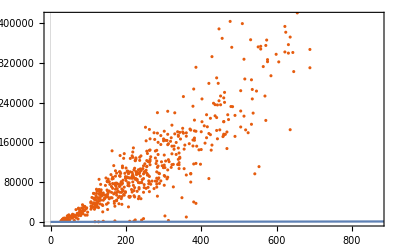

```mathematica
Do[
Print[experiments[[i]],", Null Organelles Excluded:"];
fitCellSizeFromOrganelles[Select[washed,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
]
```